(*We consider an effective Lagrangian for a charge 5/3 scalar leptoquark coupling with a lepton and a quark, where λLtauc,λRtauc,λLtaut,and λRtaut stand for the left-and right-LQ couplings with the tau and the c and t quarks. The program calculates the branching ratio for the top quark rare decay t->cγγ from the one-loop contribution from a scalar leptoquark with electric charge of 5/3 and the tau lepton. The contribution of the muon is neglected as its couplings to the leptoquark and the c and t quarks are strongly constrained by the muon anomaly and the τ->cγ decay.  The program needs the LoopTools package (https://feynarts.de/looptools/) to evaluate the Passarino-Veltman scalar 
functions. *)

(*This is the directory where all program files and results are saved. It must be changed accordingly*)

```mathematica
dircalc="C:\\Users\\980022766\\Mi unidad (gitavaresve@gmail.com)\\fi-fjVV-Decay\\Calculos_Finales";
```

```mathematica
SetDirectory[dircalc];
```

(*If the program is not run under windows comment the following cell*)

```mathematica
Install[LinkConnect["LoopTools"]];
```

====================================================
   FF 2.0, a package to evaluate one-loop integrals
 written by G. J. van Oldenborgh, NIKHEF-H, Amsterdam
 ====================================================
 for the algorithms used see preprint NIKHEF-H 89/17,
 'New Algorithms for One-loop Integrals', by G.J. van
 Oldenborgh and J.A.M. Vermaseren, published in 
 Zeitschrift fuer Physik C46(1990)425.
 ====================================================

(*If the program is run under linux or mac uncomment the following cell to install LoopTools*)

```mathematica
(*Install["LoopTools"]*)
```

(*Square amplitude for the t→cγγ decay*)

(*Loading the definitions code*)

```mathematica
<<DecayWidthDefinitions.wl;
```

(*Code to obtain the plot of Fig. 7 of manuscript*)

```mathematica
{mt=175,mμ=0.105,mτ=1.77};
```

```mathematica
{mi=mt,Qj=2/3,Qk=-1,yμ=mμ/mi;
yτ=mτ/mi,α=1/128};
```

```mathematica
mS1=1000;
```

```mathematica
Γt=1.4;
```

```mathematica
widthsRR={};Do[AppendTo[widthsRR,{mS2,DecayWidth[mS2,0, 1, 0, 1]}],{mS2,1000,2000,50}];
```

```mathematica
BRsRR=Table[{widthsRR[[i]][[1]]/1000.,widthsRR[[i]][[2]]/(Γt 10^-11)},{i,1,Length[widthsRR]}];
```

```mathematica
widthsLL={};Do[AppendTo[widthsLL,{mS2,DecayWidth[mS2,1,0,1,0]}],{mS2,1000,2000,50}];
```

```mathematica
BRsRR=Table[{widthsRR[[i]][[1]]/1000.,widthsRR[[i]][[2]]/(Γt 10^-11)},{i,1,Length[widthsRR]}];
```

```mathematica
BRsLL=Table[{widthsLL[[i]][[1]]/1000.,widthsLL[[i]][[2]]/(Γt 10^-11)},{i,1,Length[widthsLL]}];
```

```mathematica
ticks={#,ToString[#]<>"×10^-11"}&/@Range[1,9];
```

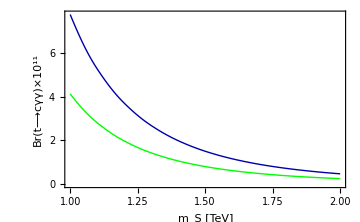

```mathematica
BRSplot=Legended[ListPlot[{BRsRR,BRsLL},Joined->True,Frame-> True,FrameLabel->{"m_S [TeV]","Br(t⟶cγγ)×10^11"},FrameStyle->Black, PlotRange->{{1,2},Automatic},InterpolationOrder->10,PlotStyle->{{Darker[Blue],Thick},{Green,Thick}},ImageSize->Medium],Placed[Framed[SwatchLegend[{Darker[Blue],Green},{"Y_(2  τ)^RLY_(3  τ)^RL≈O(1), Y_(2  τ)^LRY_(3  τ)^LR≪O(1)","Y_(2  τ)^LRY_(3  τ)^LR≈O(1), Y_(2  τ)^RLY_(3  τ)^RL≪O(1)"},LabelStyle->Small,LegendLayout->"Column"]],{0.7,0.8}]]
```